```mathematica
SetDirectory[NotebookDirectory[]];
w=Flatten@Import["w.dat"];
vsq=Flatten@Import["vsq.dat"];
expSD[t_]:=ⅇ^(-1*Total[Table[4 vsq[[i]]/(w[[i]]^2 π)(Coth[w[[i]]/(2*9.5*10^-4)]( 1-Cos[w[[i]]t])-ⅈ Sin[w[[i]]t]),{i,Length[w]}]]);
```

```mathematica
k[e_]:=2*(5*10^-5)^2 Re@NIntegrate[expSD[t]*ⅇ^(ⅈ e t),{t,0,1000}];
Plot[k[e],{e,0.015,0.03}]
```

$Aborted

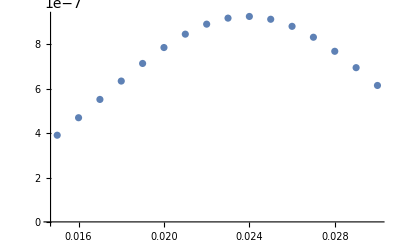

```mathematica
ListPlot@Table[{e,2*(5*10^-5)^2 NIntegrate[Re[expSD[t]*ⅇ^(-ⅈ e t)],{t,0,1000}]},{e,0.015,0.03,0.001}]
```

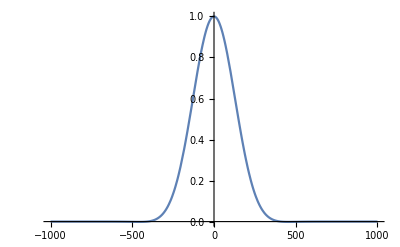

```mathematica
Plot[Re@(expSD[t]*ⅇ^(-ⅈ 0.02 t)),{t,-1000,1000},PlotRange->All]
```

```mathematica
2*(5*10^-5)^2 Re@Total@Table[expSD[t]*ⅇ^(ⅈ 0.02 t)*0.1,{t,0,1000,0.1}]
```

2.50001×10^-10

```mathematica
(* 0 K*)
```